## Finding b

We have C(T,0)=V b/T^2 for C the specific heat. The molar specific heat capacity is then C_M(T,0)=V_M b/T^2 for V_M the molar volume: V_M=M_M/ρ. We are given C_M(T,0)/R, so we rewrite this as C_M(T,0)/R=V_M b/(R T^2).

First, let’s find V_M:

```mathematica
MM=499.40 LinguisticAssistant LinguisticAssistant;
```

```mathematica
ρ=1.7 LinguisticAssistant/LinguisticAssistant;
```

```mathematica
VM=MM/ρ
```

293.765

We want a dimensionless temperature for the fitting, so we rewrite our equation as

```mathematica
Subscript[C, M]/R==(Subscript[V, M] b)/(R (T K)^2)==(Subscript[V, M](b/K^2))/R 1/T^2
```

Thus, in fitting to p/T^2, we will really be solving for V_M b/(R K^2). Let’s do the fitting.

Data points ( {T [K],C_M(T)/R} ):

```mathematica
cmdata={
{0.2,0.26},{0.25,0.19}
}; (*Using only two data points to stay within the Curie regime*)
```

```mathematica
bDimless=Fit[cmdata,{1/T^2},T]
```

0.0108286/T^2

Now the real b is the solution to

```mathematica
Clear[b];b=(b/.Solve[bDimless==(VM b)/(LinguisticAssistant Quantity[1,"Kelvins"]^2),b])⟦1⟧T^2
```

306.483

The Quantity statement is necessary to prevent Mathematica from getting confused about Kelvins versus Kelvins difference, which is sort of pathetic.

Quick unit check:

```mathematica
(VM b)/(LinguisticAssistant Quantity[1,"Kelvins"]^2)
```

0.0108286

This is dimensionless—good.

## Finding a

I think—and I could be wrong—that T≈T^* at higher temperatures (relative to the Curie temperature). If that’s correct, then the first few rows of table 1 are useful: from the bottom of 451 in Reif, we should have

```mathematica
SuperStar[T]/Subscript[T, i]==((b+a Subscript[H, f]^2)/(b+a Subscript[H, i]^2))^(1/2)
```

Here’s the table of (T_i [K],T^* [K],H_i [kG]):

```mathematica
httdata={
{0.983,0.591,1.198},
{0.977,0.461,1.675},
{0.970,0.461,2.35},
{0.972,0.264,3.14},
{0.973,0.214,3.76}
};
```

I’ll use the table down to 0.2 K, as I don’t trust this beyond there. Assume H_f=0.

We need to correct the dimensions somewhat, because we need to supply something dimensionless to FindFit. Primarily, note that since

```mathematica
bUnits=QuantityUnit[b]
```

(Kelvins Kilograms)/(Meters Moles Seconds^2)

We can divide off the units and write

```mathematica
(b/(b+a Hi^2))^(1/2)==(QuantityMagnitude[b]/(QuantityMagnitude[b]+a/bUnits (Hi kG)^2))^(1/2)
```

```mathematica
(b/(b+a Hi^2))^(1/2)==(QuantityMagnitude[b]/(QuantityMagnitude[b]+(a kG^2)/bUnits Hi^2))^(1/2)
```

We will pretend that the coefficient of H_i is a, but really we will be solving for a kG^2/(bUnits).

Before we FindFit, we’ll need to get an approximate idea of what a should be so that we can provide a reasonable initial value. To make this work, I’ve multiplied a by 10^-6, which means we need to keep track of that as part of its units.

```mathematica
Manipulate[Show[Plot[(QuantityMagnitude[b]/(QuantityMagnitude[b]+10^6 a Hi^2))^(1/2),{Hi,0,4}],ListPlot[{#⟦3⟧,#⟦2⟧/#⟦1⟧}&/@httdata]],{a,0,0.001}]
```

From this, it looks like a≈0.0003.

```mathematica
aDimless=a/.FindFit[{#⟦3⟧,#⟦2⟧/#⟦1⟧}&/@httdata,(QuantityMagnitude[b]/(QuantityMagnitude[b]+10^6 a Hi^2))^(1/2),{{a,0.00003}},Hi]
```

0.000331447

Of course, then the real a is given by solving

```mathematica
Clear[a];a=a/.Solve[(a LinguisticAssistant^2)/(b/QuantityMagnitude[b])==10^6 aDimless,a]⟦1⟧
```

33144.7

## Minimum temperature

Assuming this model works out, we can plot the minimum temperature (starting from 1.5 K) as a function of the initial magnetic field. First, let’s do a quick verification:

```mathematica
Subscript[T, f]==(b/(b+a (Hi LinguisticAssistant)^2))^(1/2)LinguisticAssistant/.{Hi->1.675}
```

T_f==0.497879

This is about what the paper reports.

```mathematica
minT[Hi_]:=QuantityMagnitude[(b/(b+a (Hi LinguisticAssistant)^2))^(1/2)LinguisticAssistant]
```

Plot will freak out about the QuantityMagnitude, so let’s define the sampling points explicitly:

```mathematica
Tpoints={#,minT[#]}&/@Table[Hi,{Hi,0,4,0.1}];
```

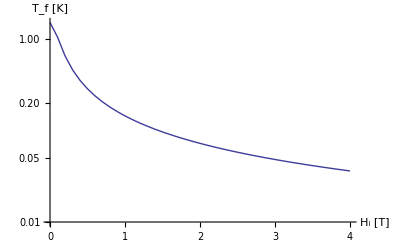

```mathematica
ListLogPlot[Tpoints,Joined->True,PlotRange->{0.01,1.5},AxesLabel->{"H_i [T]","T_f [K]"}]
```

## Heat between base and bath

Now we work out how much heat it would take (per mole) to bring the salt back up from the base temperature to the bath temperature. Here we use

```mathematica
VM b
```

0.090034

```mathematica
CM[T_]:=(VM b)/T^2
```

Now, we have C_M(T)=δQ/dT, so

```mathematica
QM=VM b∫_Subscript[T, base]^Subscript[T, bath] 1/T^2 ⅆT//FullSimplify[#,Assumptions->{Subscript[T, bath]>0,Subscript[T, base]>0,Subscript[T, bath]>Subscript[T, base]}]&
```

(0.090034) (1/T_base-1/T_bath)

```mathematica
QMdiff[Tbase_,Tbath_]:=QM/.{Subscript[T, base]->Quantity[Tbase,"Kelvins"],Subscript[T, bath]->Quantity[Tbath,"Kelvins"]}
```

For example:

```mathematica
QMdiff[0.1,1.5]
```

0.840317

```mathematica
UnitConvert[0.8403174862474466,"J/mol"]
```

0.840317

Let’s tabulate this and plot it, assuming a constant bath temperature.

```mathematica
Qpoints={#,QuantityMagnitude[QMdiff[#,1.5]]}&/@Table[Tbase,{Tbase,0.05,1.5,0.03}];
```

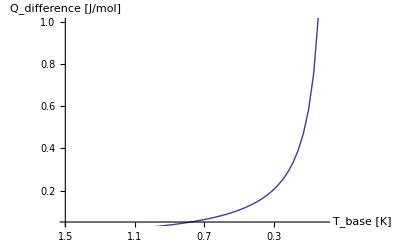

```mathematica
d=Transpose@Qpoints;
ListPlot[Transpose@{Reverse@d[[1]],d[[2]]},Ticks->{Transpose@{Range[0,1.5,0.2],Range[1.5,0,-0.2]},Automatic},Joined->True,AxesLabel->{"T_base [K]","Q_difference [J/mol]"},PlotRange->{0.05,1}]
```